# Right-Triangle Directional Zero-Friction Derivation

## This notebook documents the Mathematica derivation used for the 30-degree right-triangle flake in the research paper <Tribology International 222, 112110 (2026)>. The calculation starts from the moire density field, integrates it over the translated right-triangle domain, simplifies the integer-xi limit, and then reproduces the normalized main-text results in Eqs. (2)-(5).

## %% 01 Density and Parameters

## The density field is the two-wave triangular-lattice expression. The moved density fmove[x, y, mx, my, theta, R01] is derived from <Zhang Z. Design of Frictionless Interfaces for Moire Layers. Phys Rev Lett 2025; 135>.

```mathematica
ClearAll["Global`*"];$Assumptions=0≤θ&&{x,y,mx,my,R01,λ,ξ,γ}∈Reals&&R01>0&&λ>0&&ξ>0&&Csc[θ/2]≥1&&Cot[θ/2]∈Reals
```

0≤θ&&(x|y|mx|my|R01|λ|ξ|γ)∈ℝ&&R01>0&&λ>0&&ξ>0&&Csc[θ/2]≥1&&Cot[θ/2]∈ℝ

```mathematica
fmove[x_,y_,mx_,my_,θ_,R01_]:=2 Cos[(2 π (my+2 y-mx Cot[θ/2]) Sin[θ/2])/R01] Cos[(2 π (mx+2 x+my Cot[θ/2]) Sin[θ/2])/(√3 R01)]+Cos[(4 π (mx+2 x+my Cot[θ/2]) Sin[θ/2])/(√3 R01)]
```

```mathematica
λ0[θ0_,R01_]:=R01/(2 Sin[θ0/2]);LatticeConstant=1.42 √3;θ0=10 °;
```

## %% 02 Area Relation

```mathematica
SRightTriangle=(√3 ξ λ 3 ξ λ)/(2 2 2);SCompleteMoire=(√3 λ^2)/2;
```

```mathematica
FullSimplify[SRightTriangle/SCompleteMoire]
```

(3 ξ^2)/4

## %% 03 Geometry Check Plot

## The moved density is shown only inside the 30-degree right-triangle integration domain.

```mathematica
ξ0=2;
```

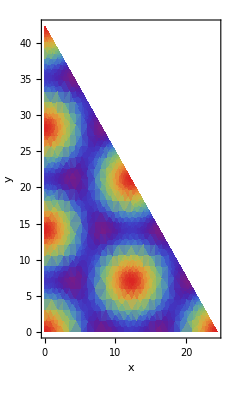

```mathematica
DensityPlot[fmove[x,y,0,0,θ0,LatticeConstant],{x,0,1/2 √3 ξ0 λ0[θ0,LatticeConstant]},{y,0,3/2 ξ0 λ0[θ0,LatticeConstant]},AxesLabel->Automatic,ColorFunction->"Rainbow",MaxRecursion->3,PlotRange->All,RegionFunction->Function[{x,y,z},y<-√3 x+3/2 ξ0 λ0[θ0,LatticeConstant]],AspectRatio->Automatic]
```

## %% 04 Eq. S2 General Energy

## Integrate the translated density over the 30-degree right-triangle domain. This calculation step will take a long time.

```mathematica
ARtriξ30Initial[mx_,my_,θ_,ξ_]=FullSimplify[∫_0^(1/2 √3 ξ λ0[θ,R01]) ∫_0^(3/2 ξ λ0[θ,R01]) fmove[x,y,mx,my,θ,R01] Boole[y<-√3 x+3/2 ξ λ0[θ,R01]]ⅆyⅆx]
```

∫_0^(1/4 √3 R01 ξ Csc[θ/2]) ∫_0^(3/4 R01 ξ Csc[θ/2]) Boole[4 (√3 x+y)<3 R01 ξ Csc[θ/2]] (2 Cos[(2 π (my+2 y-mx Cot[θ/2]) Sin[θ/2])/R01] Cos[(2 π (mx+2 x+my Cot[θ/2]) Sin[θ/2])/(√3 R01)]+Cos[(4 π (mx+2 x+my Cot[θ/2]) Sin[θ/2])/(√3 R01)])ⅆyⅆx

## Next rotate the displacement components into the substrate-frame variables used in the paper.

```mathematica
ARtriξ30Rotated[mx_,my_,θ_,ξ_]=FullSimplify[ARtriξ30Initial[mx Cos[-θ/2]-my Sin[-θ/2],my Cos[-θ/2]+mx Sin[-θ/2],θ,ξ]]
```

1/(64 π^2)√3 R01^2 Csc[θ/2]^2 (3 Cos[(4 my π)/(√3 R01)]-3 Cos[(4 my π)/(√3 R01)+2 π ξ]+16 Cos[(2 my π)/(√3 R01)+π FractionalPart[ξ/2]] Sin[(2 mx π)/R01] Sin[π FractionalPart[ξ/2]]-2 Sin[π ξ] (Sin[(2 (3 mx+√3 my) π)/(3 R01)]-2 Sin[(2 π (-3 mx+√3 my+3 R01 ξ))/(3 R01)]+Sin[(π (6 mx+2 √3 my-9 R01 ξ+6 R01 FractionalPart[ξ/2]))/(3 R01)])-6 π ξ (Sin[(4 my π)/(√3 R01)+2 π ξ]-2 Cos[(4 my π)/(√3 R01)+π FractionalPart[ξ]] Sin[π FractionalPart[ξ]]))

## Finally divide by lambda0[theta, R01]^2 and multiply by lambda^2. This produces Eq. S2 in the form ARtri xi 30[mx, my, lambda, xi].

```mathematica
ARtriξ30[mx_,my_,λ_,ξ_]=FullSimplify[ARtriξ30Rotated[mx,my,θ,ξ]/λ0[θ,R01]^2] λ^2
```

1/(16 π^2)√3 λ^2 (3 Cos[(4 my π)/(√3 R01)]-3 Cos[(4 my π)/(√3 R01)+2 π ξ]+16 Cos[(2 my π)/(√3 R01)+π FractionalPart[ξ/2]] Sin[(2 mx π)/R01] Sin[π FractionalPart[ξ/2]]-2 Sin[π ξ] (Sin[(2 (3 mx+√3 my) π)/(3 R01)]-2 Sin[(2 π (-3 mx+√3 my+3 R01 ξ))/(3 R01)]+Sin[(π (6 mx+2 √3 my-9 R01 ξ+6 R01 FractionalPart[ξ/2]))/(3 R01)])-6 π ξ (Sin[(4 my π)/(√3 R01)+2 π ξ]-2 Cos[(4 my π)/(√3 R01)+π FractionalPart[ξ]] Sin[π FractionalPart[ξ]]))

## %% 05 Integer xi: From Eq. S2 to Eq. S3

## When xi is an integer, Sin[pi xi] and Sin[2 pi xi] vanish, Cos[2 pi xi] becomes one, and FractionalPart[xi] becomes zero. The only remaining parity information is FractionalPart[xi/2], which is zero for even xi and one-half for odd xi.

```mathematica
integerRules={Sin[π ξ]->0,Sin[2 π ξ]->0,Cos[2 π ξ]->1,FractionalPart[ξ]->0};
```

```mathematica
eqS2IntegerStep=FullSimplify[ARtriξ30[mx,my,λ,ξ]/.integerRules]
```

(√3 λ^2 (3 Cos[(4 my π)/(√3 R01)]-3 Cos[(4 my π)/(√3 R01)+2 π ξ]-6 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ]+16 Cos[(2 my π)/(√3 R01)+π FractionalPart[ξ/2]] Sin[(2 mx π)/R01] Sin[π FractionalPart[ξ/2]]))/(16 π^2)

## This compact expression is Eq. S3. The parity-dependent term is intentionally kept as FractionalPart[xi/2].

```mathematica
ARtriξ30N[mx_,my_,λ_,ξ_]=FullSimplify[eqS2IntegerStep]
```

(√3 λ^2 (3 Cos[(4 my π)/(√3 R01)]-3 Cos[(4 my π)/(√3 R01)+2 π ξ]-6 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ]+16 Cos[(2 my π)/(√3 R01)+π FractionalPart[ξ/2]] Sin[(2 mx π)/R01] Sin[π FractionalPart[ξ/2]]))/(16 π^2)

## %% 06 Main-Text Eqs. (2)-(5)

## The normalized energy uses the triangle area 3 sqrt(3) xi^2 lambda^2/8. The force expressions below use the directional derivative along gamma, matching the main-text convention.

```mathematica
areaNormalizer=3/8 √3 ξ^2 λ^2;
```

```mathematica
ARtriξ30NOdd[mx_,my_,λ_,ξ_]=FullSimplify[ARtriξ30N[mx,my,λ,ξ]/.FractionalPart[ξ/2]->1/2]
```

-(√3 λ^2 (-3 Cos[(4 my π)/(√3 R01)]+3 Cos[(4 my π)/(√3 R01)+2 π ξ]+16 Sin[(2 mx π)/R01] Sin[(2 my π)/(√3 R01)]+6 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ]))/(16 π^2)

```mathematica
ARtriξ30NEven[mx_,my_,λ_,ξ_]=FullSimplify[ARtriξ30N[mx,my,λ,ξ]/.FractionalPart[ξ/2]->0]
```

-(3 √3 λ^2 (-Cos[(4 my π)/(√3 R01)]+Cos[(4 my π)/(√3 R01)+2 π ξ]+2 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ]))/(16 π^2)

## Eq. (2): normalized energy for odd integer xi.

```mathematica
FullSimplify[ARtriξ30NOdd[mx,my,λ,ξ]/areaNormalizer]
```

-(-3 Cos[(4 my π)/(√3 R01)]+3 Cos[(4 my π)/(√3 R01)+2 π ξ]+16 Sin[(2 mx π)/R01] Sin[(2 my π)/(√3 R01)]+6 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ])/(6 π^2 ξ^2)

## Eq. (3): normalized energy for even integer xi.

```mathematica
FullSimplify[ARtriξ30NEven[mx,my,λ,ξ]/areaNormalizer]
```

-(-Cos[(4 my π)/(√3 R01)]+Cos[(4 my π)/(√3 R01)+2 π ξ]+2 π ξ Sin[(4 my π)/(√3 R01)+2 π ξ])/(2 π^2 ξ^2)

## Eq. (4): directional force for odd integer xi.

```mathematica
FullSimplify[-D[ARtriξ30NOdd[mx,my,λ,ξ], mx] Cos[γ]-D[ARtriξ30NOdd[mx,my,λ,ξ], my] Sin[γ]]
```

(λ^2 (4 √3 Cos[(2 mx π)/R01] Cos[γ] Sin[(2 my π)/(√3 R01)]+Sin[γ] (3 π ξ Cos[(4 my π)/(√3 R01)+2 π ξ]+4 Cos[(2 my π)/(√3 R01)] Sin[(2 mx π)/R01]-3 Cos[(4 my π)/(√3 R01)+π ξ] Sin[π ξ])))/(2 π R01)

## Eq. (5): directional force for even integer xi.

```mathematica
FullSimplify[-D[ARtriξ30NEven[mx,my,λ,ξ], mx] Cos[γ]-D[ARtriξ30NEven[mx,my,λ,ξ], my] Sin[γ]]
```

(3 λ^2 Sin[γ] (π ξ Cos[(4 my π)/(√3 R01)+2 π ξ]-Cos[(4 my π)/(√3 R01)+π ξ] Sin[π ξ]))/(2 π R01)